Initial Graph:

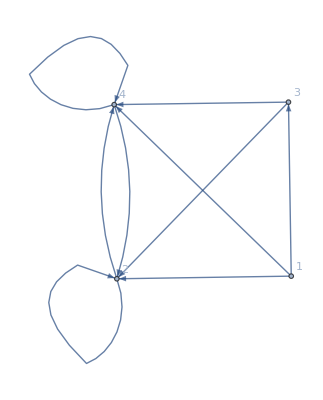

Frequency Vector: {{{1,γ/(1-γ^2),0,γ^2/(1-γ^2)},{1,γ,0,γ^2/(1-γ)},{1,γ/(1-γ),0,0},{1,γ^2/(1-γ^2),γ,γ^3/(1-γ^2)},{1,γ^2,γ,γ^3/(1-γ)},{1,γ^2/(1-γ),γ,0},{1,γ^3/(1-γ^2),γ,γ^2/(1-γ^2)},{1,γ^3/(1-γ),γ,γ^2},{1,0,γ,γ^2/(1-γ)},{1,γ^2/(1-γ^2),0,γ/(1-γ^2)},{1,γ^2/(1-γ),0,γ},{1,0,0,γ/(1-γ)}},{{0,1/(1-γ^2),0,γ/(1-γ^2)},{0,1,0,γ/(1-γ)},{0,1/(1-γ),0,0}},{{0,γ/(1-γ^2),1,γ^2/(1-γ^2)},{0,γ,1,γ^2/(1-γ)},{0,γ/(1-γ),1,0},{0,γ^2/(1-γ^2),1,γ/(1-γ^2)},{0,γ^2/(1-γ),1,γ},{0,0,1,γ/(1-γ)}},{{0,γ/(1-γ^2),0,1/(1-γ^2)},{0,γ/(1-γ),0,1},{0,0,0,1/(1-γ)}}}

#############################################################################################

Equation List: {r[1]+(γ r[2])/(1-γ^2)+(γ^2 r[4])/(1-γ^2),r[1]+γ r[2]+(γ^2 r[4])/(1-γ),r[1]+(γ r[2])/(1-γ),r[1]+(γ^2 r[2])/(1-γ^2)+γ r[3]+(γ^3 r[4])/(1-γ^2),r[1]+γ^2 r[2]+γ r[3]+(γ^3 r[4])/(1-γ),r[1]+(γ^2 r[2])/(1-γ)+γ r[3],r[1]+(γ^3 r[2])/(1-γ^2)+γ r[3]+(γ^2 r[4])/(1-γ^2),r[1]+(γ^3 r[2])/(1-γ)+γ r[3]+γ^2 r[4],r[1]+γ r[3]+(γ^2 r[4])/(1-γ),r[1]+(γ^2 r[2])/(1-γ^2)+(γ r[4])/(1-γ^2),r[1]+(γ^2 r[2])/(1-γ)+γ r[4],r[1]+(γ r[4])/(1-γ)}

Dominated ... TODO

Dominated ... TODO

Dominated ... TODO

«5 more identical outputs»

Non-Dominated Equation List: {r[1]+(γ r[2])/(1-γ),r[1]+(γ^2 r[2])/(1-γ)+γ r[3],r[1]+γ r[3]+(γ^2 r[4])/(1-γ),r[1]+(γ r[4])/(1-γ)}

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 1

Inequalities used: r[3]<r[2]&&r[4]<r[2]

Integration: γ/(4-4 γ)

Measure: 1/3

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 2

Inequalities used: r[3]>r[2]&&r[4]<r[2]

Integration: ((-3+γ) γ)/(24 (-1+γ))

Measure: 1/6

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 3

Inequalities used: r[2]<r[4]<r[3]

Integration: ((-3+γ) γ)/(24 (-1+γ))

Measure: 1/6

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 4

Inequalities used: (r[3]>r[2]||r[4]>r[2])&&(r[3]≤r[2]||r[4]>r[3])

Integration: γ/(4-4 γ)

Measure: 1/3

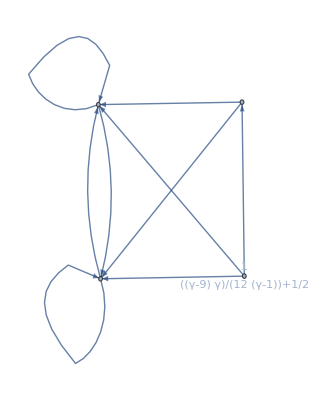

```mathematica
(*Be sure to run "runThisFileFirst.nb"*)
(*To Run, press Shift+Enter. Or, at top, Evaluation -> Evaluate Cells*)
(*Note: If running forever,(usually #states > 7), then Evaluation -> Quit Kernal -> local*)
vertexAndNodes = {1->2,1->3, 2->3, 3->4, 4->4};
vertexAndNodes = {1->2,1->3, 2->3, 3->4, 4->4};
vertexAndNodes = {1->2,1->4, 2->3, 2->1, 2->3, 2->6, 3->1, 3->2, 3->5, 4->1, 4->5, 4->6, 5->3, 5->6, 5->4, 6->2, 6->4, 6->5};
vertexAndNodes = {1->5, 5->6, 6->1, 1->2, 2->3, 3->4, 4->2, 2->2}; (*This one breaks it*)
vertexAndNodes = {1->2,1->3,1->4, 2->2, 2->4, 4->2, 3->2, 3->4, 4->4}; 
(*            graph    , First/All, None/Basic/Measure*)
powerOfGraph[vertexAndNodes, "First", "Basic"]

(*
First - calculate Power for first state only;
All - Calcuate Power for all states;
None - Display only final power graph;
Basic - Display basic info such as frequency vector, inequalities, and integrations.;
Measure - Display Measure and power graph. Only works with "First";
*)

(*If you'd like to compare a handwritten equation with the calculated power:*)
eq = 2/3*γ + 5/12*γ^2 + 7/12*γ^3 + 1/2 *γ^4/(1-γ);
powerCheck[eq];
(*Note: use the ";" at the end to suppress output*)
```

```mathematica
-
```

```mathematica
eqList = equationList[[5;;12]];
eqList = equationList;
frequencies = Length[eqList];
frequency = frequencies;
inList = {};
For[fInd= 1, fInd≤ frequencies, fInd++,
If[fInd ≠ frequency,
AppendTo[inList, eqList[[frequency]] >   eqList[[fInd]]];
,
];
];
AppendTo[inList,  0 <  γ< 1];
inList
Clear[γ,r, $Assumptions]
inList //Simplify
output = FullSimplify[Reduce[inList,hyperCubeVariables, Reals] /._Equal->False];
output
```

{r[1]+(γ r[4])/(1-γ)>r[1]+(γ r[2])/(1-γ^2)+(γ^2 r[4])/(1-γ^2),r[1]+(γ r[4])/(1-γ)>r[1]+γ r[2]+(γ^2 r[4])/(1-γ),r[1]+(γ r[4])/(1-γ)>r[1]+(γ r[2])/(1-γ),r[1]+(γ r[4])/(1-γ)>r[1]+(γ^2 r[2])/(1-γ^2)+γ r[3]+(γ^3 r[4])/(1-γ^2),r[1]+(γ r[4])/(1-γ)>r[1]+γ^2 r[2]+γ r[3]+(γ^3 r[4])/(1-γ),r[1]+(γ r[4])/(1-γ)>r[1]+(γ^2 r[2])/(1-γ)+γ r[3],r[1]+(γ r[4])/(1-γ)>r[1]+(γ^3 r[2])/(1-γ^2)+γ r[3]+(γ^2 r[4])/(1-γ^2),r[1]+(γ r[4])/(1-γ)>r[1]+(γ^3 r[2])/(1-γ)+γ r[3]+γ^2 r[4],r[1]+(γ r[4])/(1-γ)>r[1]+γ r[3]+(γ^2 r[4])/(1-γ),r[1]+(γ r[4])/(1-γ)>r[1]+(γ^2 r[2])/(1-γ^2)+(γ r[4])/(1-γ^2),r[1]+(γ r[4])/(1-γ)>r[1]+(γ^2 r[2])/(1-γ)+γ r[4],0<γ<1}

{r[4]>r[2],r[4]>r[2],r[4]>r[2],γ^2 r[3]+r[4]+γ r[4]>γ r[2]+r[3]+γ^2 r[4],(1+γ) r[4]>γ r[2]+r[3],γ r[3]+r[4]>γ r[2]+r[3],γ^2 (-r[2]+r[3])+r[4]>r[3],γ r[3]+r[4]+γ^2 r[4]>γ^2 r[2]+r[3]+γ r[4],r[4]>r[3],r[4]>r[2],r[4]>r[2],True}

1+2 γ≠√5&&(r[3]>r[2]||r[4]>r[2])&&(r[3]≤r[2]||r[4]>r[3])

```mathematica
Clear[x1,x2,y]
eq1 = -y^2*x1 -y*x1 + x1 //Simplify
y = 1/2 (-1+√5);
y*y +y//Simplify //N
(x2 -1/2 (-1+√5))^2 //Expand //Simplify
eq2 = -1+y+y^2;
```

-x1 (-1+y+y^2)

1.

3/2-(√5)/2+x2-√5 x2+x2^2

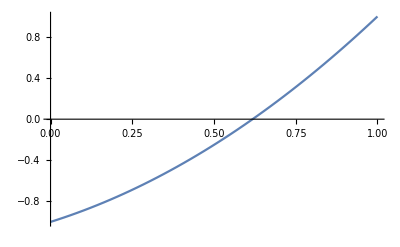

```mathematica
Plot[-1+y+y^2, {y, 0,1}]
```

```mathematica
Reduce[1>γ>0&&First@region,hyperCubeVariables]/._Equal->False
```

(0<γ<1/2&&((0<r[1]≤γ&&0≤r[2]<-r[1]/(-1+γ)&&0≤r[3]<(r[1]-r[2]+γ r[2])/γ)||(γ<r[1]<1-γ&&((0≤r[2]<(γ-r[1])/(-1+γ)&&0≤r[3]≤1)||((γ-r[1])/(-1+γ)<r[2]<-r[1]/(-1+γ)&&0≤r[3]<(r[1]-r[2]+γ r[2])/γ)))||(1-γ<r[1]≤1&&((0≤r[2]<(γ-r[1])/(-1+γ)&&0≤r[3]≤1)||((γ-r[1])/(-1+γ)<r[2]≤1&&0≤r[3]<(r[1]-r[2]+γ r[2])/γ)))))||(1/2<γ<1&&((0<r[1]<1-γ&&0≤r[2]<-r[1]/(-1+γ)&&0≤r[3]<(r[1]-r[2]+γ r[2])/γ)||(1-γ<r[1]<γ&&0≤r[2]≤1&&0≤r[3]<(r[1]-r[2]+γ r[2])/γ)||(γ<r[1]≤1&&((0≤r[2]<(γ-r[1])/(-1+γ)&&0≤r[3]≤1)||((γ-r[1])/(-1+γ)<r[2]≤1&&0≤r[3]<(r[1]-r[2]+γ r[2])/γ)))))